```mathematica
Charting`$InteractiveHighlighting=False
```

False

## Data 3 to 7

```mathematica
data=Join[Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL000``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"t (s)"->1,"V (V)"->2|>]&/@Range[1,9],Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL00``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"t (s)"->1,"V (V)"->2|>]&/@Range[10,17]];
```

```mathematica
Length@data
```

17

```mathematica
data3to7=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{3,7}];
```

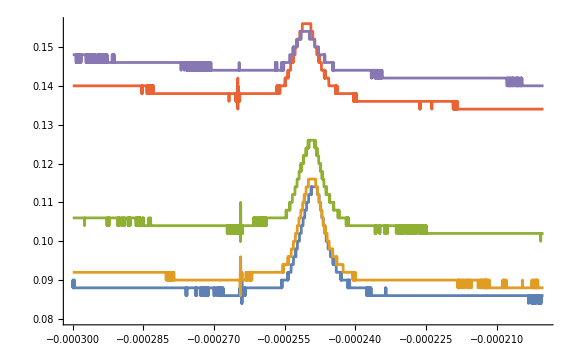

```mathematica
ListLinePlot[data3to7,ImageSize->Large]
```

```mathematica
Length@First@data3to7
```

5000

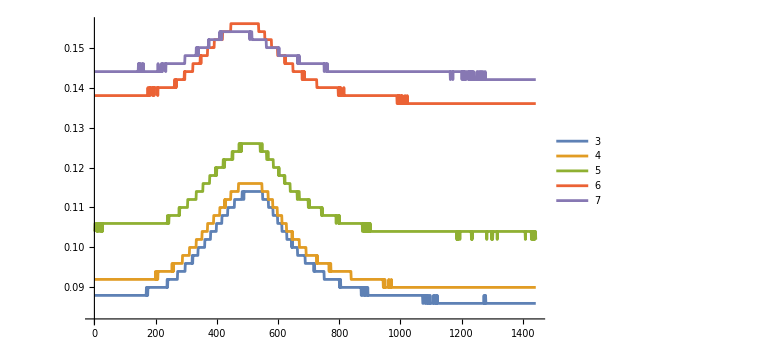

```mathematica
fd3to7=Take[Transpose[Take[#1,#2]][[2]],{550,1991}]&@@@Transpose[{data3to7,{{1500,3500},{1485,3500},{1480,3500},{1445,3500},{1460,3500}}}]//Evaluate;
ListLinePlot[fd3to7,ImageSize->Large,PlotLegends->Placed[Range[3,7],Below]]
```

```mathematica
gf=NonlinearModelFit[#,a Exp[(-(x-x0)^2)/(2 σ^2)]+b x+c,{a,{x0,500},σ,b,c},x,AccuracyGoal->5,MaxIterations->1000]&/@fd3to7
```

{FittedModel[0.0884417+0.0253474 ⅇ^(-0.0000290056 («1»)^2)-1.37494×10^-6 x],FittedModel[0.0920864+0.0242318 ⅇ^(-0.0000314028 («1»)^2)-1.47698×10^-6 x],FittedModel[0.105826+0.0202313 ⅇ^(-0.0000326895 («1»)^2)-1.46026×10^-6 x],FittedModel[0.138307+0.0182683 ⅇ^(-0.0000320633 («1»)^2)-1.55599×10^-6 x],FittedModel[0.144339+0.00995104 ⅇ^(-0.0000341448 («1»)^2)-9.6179×10^-7 x]}

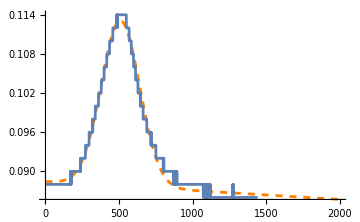
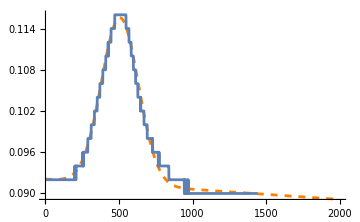
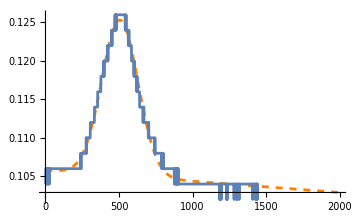
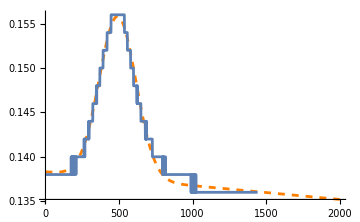
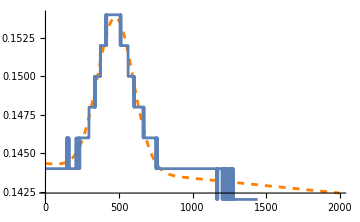

```mathematica
Show[Plot[#2["BestFit"],{x,0,2000},PlotRange->All,PlotStyle->{Dashed,Orange}],ListLinePlot[#1,PlotRange->All],PlotRange->All,ImageSize->Medium]&@@@Transpose[{fd3to7,gf}]
```

```mathematica
lc={#["BestFitParameters"][[4]][[2]],#["BestFitParameters"][[5]][[2]]}&/@gf
```

{{-1.37494×10^-6,0.0884417},{-1.47698×10^-6,0.0920864},{-1.46026×10^-6,0.105826},{-1.55599×10^-6,0.138307},{-9.6179×10^-7,0.144339}}

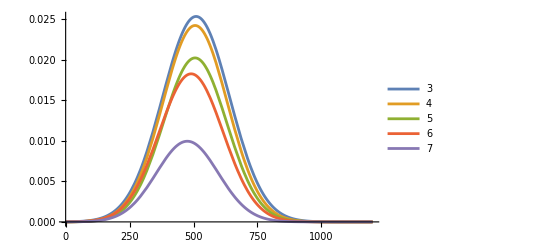

```mathematica
Plot[(#1["BestFit"]-#2[[1]]x-#2[[2]])&@@@Transpose[{gf,lc}]//Evaluate,{x,0,1200},PlotLegends->Range[3,7]]
```

## Data 8 to 12

```mathematica
data8to12=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{8,12}];
```

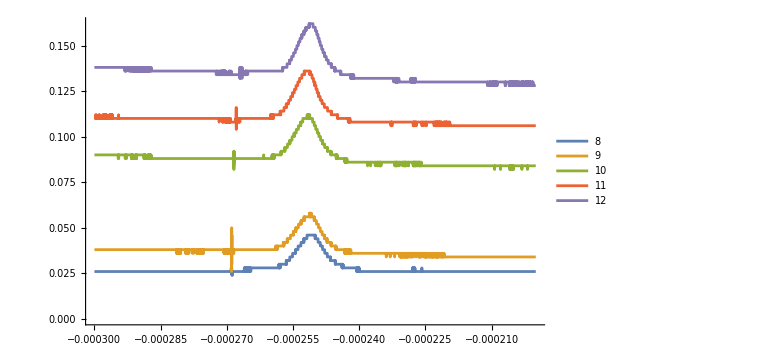

```mathematica
ListLinePlot[data8to12,ImageSize->Large,PlotLegends->Placed[Range[8,12],Below]]
```

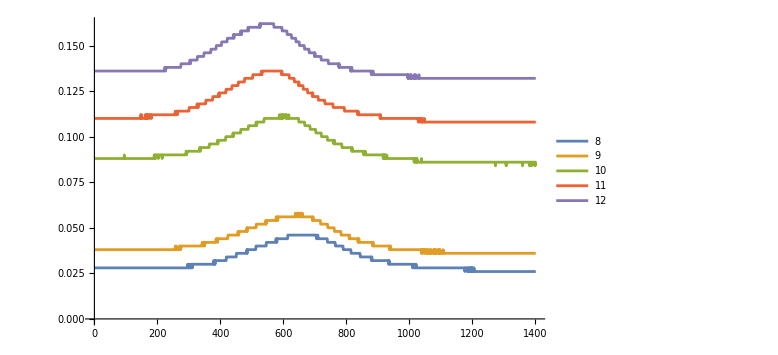

```mathematica
fd8to12=Take[Transpose[Take[#1,#2]][[2]],{800,2200}]&@@@Transpose[{data8to12,{{997,3500},{1000,3500},{1025,3500},{1050,3500},{1110,3500}}}]//Evaluate;
ListLinePlot[fd8to12,ImageSize->Large,PlotLegends->Placed[Range[8,12],Below]]
```

```mathematica
gf2=NonlinearModelFit[#,a Exp[(-(x-x0)^2)/(2 σ^2)]+b x+c,{a,{x0,600},σ,b,c},x,AccuracyGoal->5,MaxIterations->1000]&/@fd8to12
```

{FittedModel[0.0280948+0.0182202 ⅇ^(-0.0000219628 («1»)^2)-1.0527×10^-6 x],FittedModel[0.0382329+0.0190542 ⅇ^(-0.0000233288 («1»)^2)-1.66221×10^-6 x],FittedModel[0.0884417+0.0229326 ⅇ^(-0.0000244054 («1»)^2)-1.87803×10^-6 x],FittedModel[0.110613+0.025508 ⅇ^(-0.0000269638 («1»)^2)-1.8014×10^-6 x],FittedModel[0.136211+0.0266138 ⅇ^(-0.0000293978 («1»)^2)-3.25957×10^-6 x]}

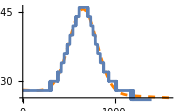
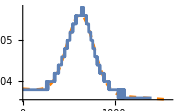
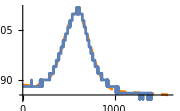
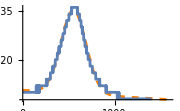
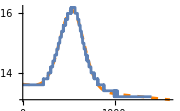

```mathematica
Show[Plot[#2["BestFit"],{x,0,1600},PlotRange->All,PlotStyle->{Dashed,Orange}],ListLinePlot[#1,PlotRange->All],PlotRange->All,ImageSize->Small]&@@@Transpose[{fd8to12,gf2}]
```

```mathematica
lc2={#["BestFitParameters"][[4]][[2]],#["BestFitParameters"][[5]][[2]]}&/@gf2
```

{{-1.0527×10^-6,0.0280948},{-1.66221×10^-6,0.0382329},{-1.87803×10^-6,0.0884417},{-1.8014×10^-6,0.110613},{-3.25957×10^-6,0.136211}}

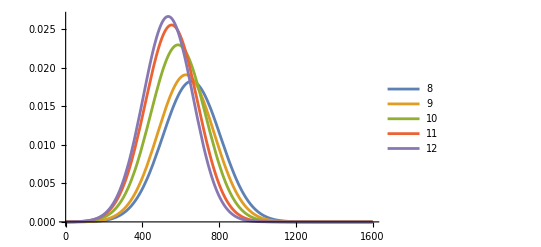

```mathematica
Plot[(#1["BestFit"]-#2[[1]]x-#2[[2]])&@@@Transpose[{gf2,lc2}]//Evaluate,{x,0,1600},PlotLegends->Range[8,12]]
```

## Data 13 to 17

```mathematica
data13to17=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{13,17}];
```

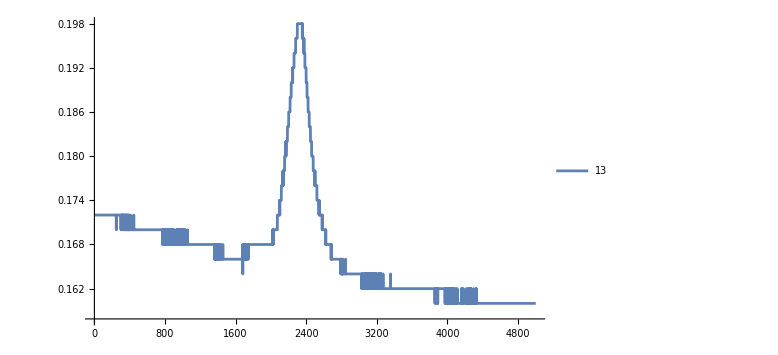
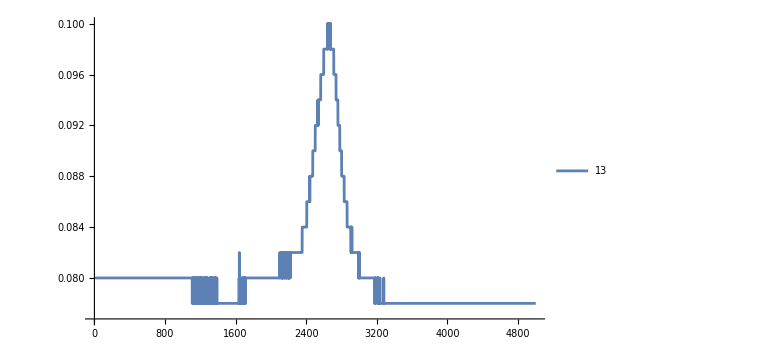
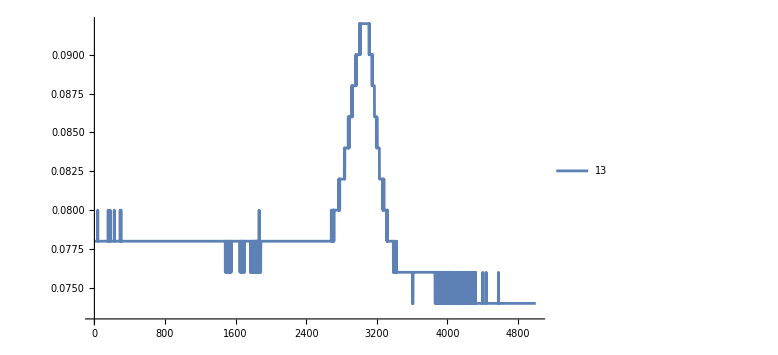
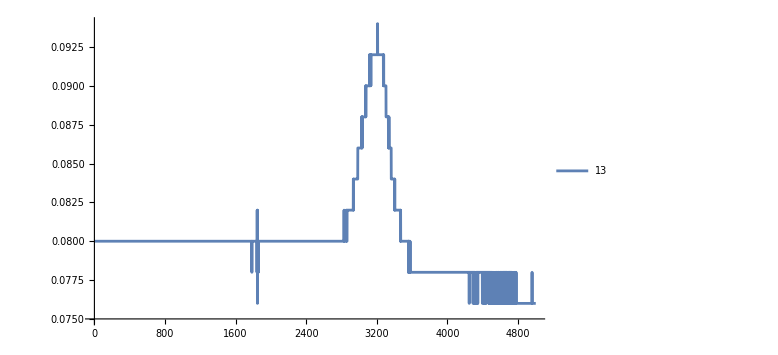
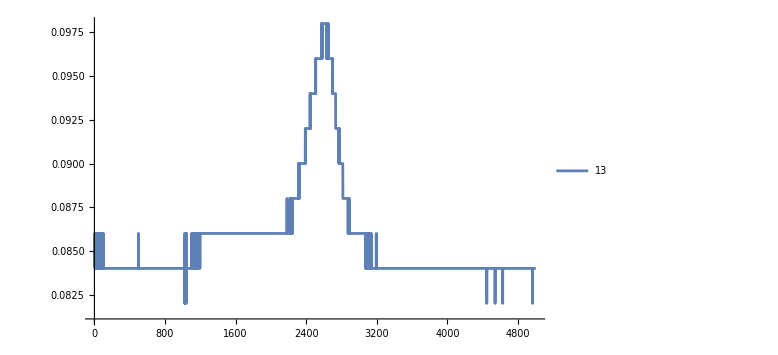

```mathematica
ListLinePlot[Transpose[#][[2]],ImageSize->Large,PlotLegends->Placed[Range[13,17],Below],PlotRange->All]&/@data13to17
```

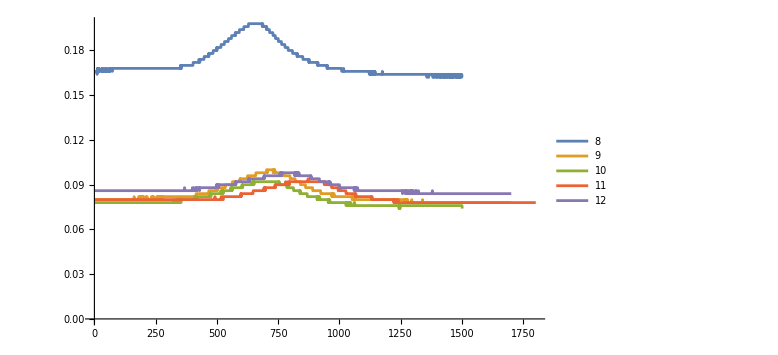

```mathematica
fd13to17=Take[Transpose[Take[#1,#2]][[2]],#3]&@@@Transpose[{data13to17,{{1671,5000},{1641,5000},{1862,5000},{1838,5000},{1016,5000}},{{1,1500},{300,2000},{500,2000},{500,2300},{800,2500}}}]//Evaluate;
ListLinePlot[fd13to17,ImageSize->Large,PlotLegends->Placed[Range[8,12],Below],PlotRange->All]
```

```mathematica
gf3=NonlinearModelFit[#1,a Exp[(-(x-x0)^2)/(2 σ^2)]+b x+c,{a,{x0,700},σ,b,c},x,AccuracyGoal->5,MaxIterations->1000]&@@@Transpose[{fd13to17}]
```

{FittedModel[0.168131+0.0304749 ⅇ^(-0.0000314945 («1»)^2)-2.8957×10^-6 x],FittedModel[0.0808659+0.018581 ⅇ^(-0.0000235795 («1»)^2)-1.64223×10^-6 x],FittedModel[0.0782815+0.0148996 ⅇ^(-0.000023483 («1»)^2)-1.83652×10^-6 x],FittedModel[0.0802606+0.0133784 ⅇ^(-0.0000219736 («1»)^2)-1.47648×10^-6 x],FittedModel[0.0862699+0.0118792 ⅇ^(-0.0000188003 («1»)^2)-1.37553×10^-6 x]}

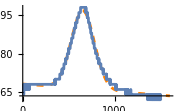
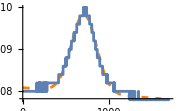
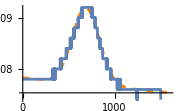
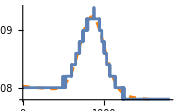
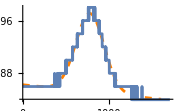

```mathematica
Show[Plot[#2["BestFit"],{x,0,1600},PlotRange->All,PlotStyle->{Dashed,Orange}],ListLinePlot[#1,PlotRange->All],PlotRange->All,ImageSize->Small]&@@@Transpose[{fd13to17,gf3}]
```

```mathematica
lc3={#["BestFitParameters"][[4]][[2]],#["BestFitParameters"][[5]][[2]]}&/@gf3
```

{{-2.8957×10^-6,0.168131},{-1.64223×10^-6,0.0808659},{-1.83652×10^-6,0.0782815},{-1.47648×10^-6,0.0802606},{-1.37553×10^-6,0.0862699}}

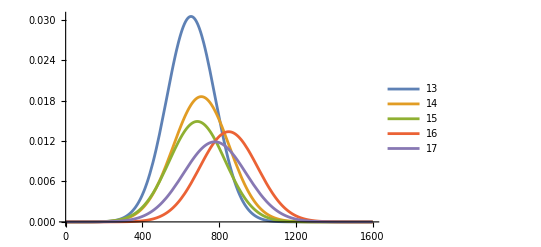

```mathematica
Plot[(#1["BestFit"]-#2[[1]]x-#2[[2]])&@@@Transpose[{gf3,lc3}]//Evaluate,{x,0,1600},PlotLegends->Range[13,17]]
```

## Last stuff IV curves

```mathematica
datalast=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL00``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,4]][All,<|"t_1 (s)"->1,"V_x (V)"->2,"t_2 (s)"->3,"V_y (V)"->4|>]&/@Range[18,19];
```

```mathematica
datalast2=Transpose[{#[All,"V_x (V)"],#[All,"V_y (V)"]}//Normal]&/@datalast;
```

```mathematica
Length@First@datalast2
```

5000

```mathematica
fit=NonlinearModelFit[First@datalast2,-a Exp[k (x-x0)]+b,{a,b,k,x0},x]
```

FittedModel[1.24089-0.00704839 ⅇ^(0.695075 (-1.53499+x))]

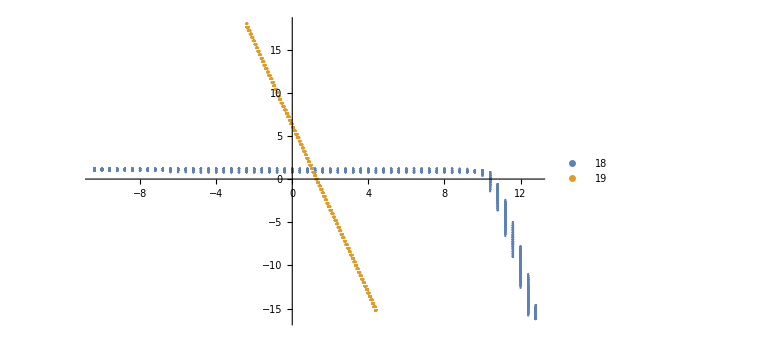

```mathematica
Show[ListPlot[datalast2,ImageSize->Large,PlotLegends->Placed[{18,19},Below],PlotRange->All](*,Plot[fit[x],{x,-10,18},ImageSize->Large,PlotStyle->{Dashed,Orange}]*)]
```